```mathematica
a=227.92*10^6
b=2.2692381163 * 10^8
T=67386816
c=(π*a*b)/T
e=0.0933941
d=(249.23*10^6*(1+e*Cos(0)))/e
```

2.2792×10^8

2.26924×10^8

67386816

2.41122×10^9

0.0933941

2.66858×10^9

```mathematica
s=NDSolve[{((e*d)^2× θ'[t])/(2(1+e*Cos[θ[t]])^2)==c,θ[0]==0},θ,{t,0,T}]
```

{{θ→InterpolatingFunction[…]}}

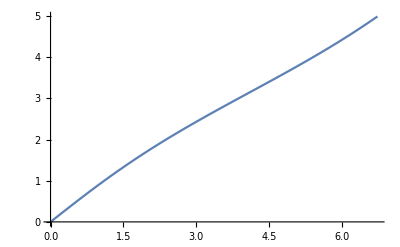

```mathematica
Plot[Evaluate[θ[t]/.s],{t,0,T},PlotRange->All]
```

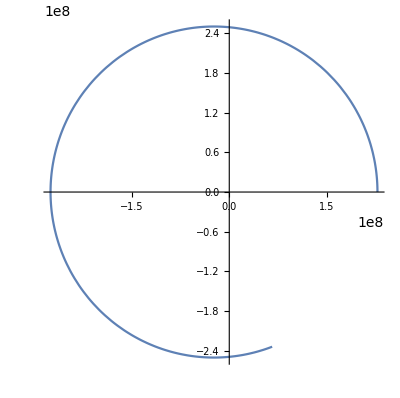

```mathematica
curv=ParametricPlot[Evaluate[CoordinateTransform["Polar"->"Cartesian",{(e*d)/(1+e*Cos[θ[t]]),θ[t]}]/.s],{t,0,T}]
```

```mathematica
u[t_]:=First[Evaluate[First[CoordinateTransform["Polar"->"Cartesian",{(e×d)/(1+e×Cos[θ[t]]),θ[t]}]]/.s]]
v[t_]:=First[Evaluate[Last[CoordinateTransform["Polar"->"Cartesian",{(e×d)/(1+e×Cos[θ[t]]),θ[t]}]]/.s]]
```

```mathematica
First[Evaluate[First[CoordinateTransform["Polar"->"Cartesian",{(e×d)/(1+e×Cos[θ[t]]),θ[t]}]]/.s]]
```

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(d e Cos[θ[t]])/(1+e Cos[θ[t]])
```

(d e Cos[θ[t]])/(1+e Cos[θ[t]])

```mathematica
Animate[Show[curv,Graphics[{PointSize[Large],Red,Point[{u[T],v[T]}]}]],{T,0,5.94×10^6}]
```